# Universidad del valle sede tuluá

## Proyecto de ecuaciones diferenciales

ingeniería en sistemas 3742

## Aplicación de las ecuaciones diferenciales para el modelado de circuitos eléctricos de primer y segundo orden

### CONCEPTOS PRELIMINARES

#### Voltaje

La palabra voltaje o potencial eléctrica, la real academia la define como “cantidad de voltios que actúan en un aparato o sistemas eléctrico” El voltaje es la capacidad física que tiene un circuito eléctrico, debido a que impulsa a los electrones a lo extenso de un conductor, esto quiere decir, que el voltio conduce la energía eléctrica con mayor o menor potencia, debido a que el voltaje es el mecanismo eléctrico entre los dos cuerpos, basándose a que si los dos puntos establecen un contacto de flujo de electrones puede suceder una transferencia de energía de ambos puntos, porque los electrones son cargas negativas y son atraídas por protones con carga positiva, pero además los electrones son rechazados entre sí por tener la misma carga.

La tensión entre dos puntos A y B es independiente del camino recorrido por la carga y depende exclusivamente del potencial eléctrico de dichos puntos A y B en el campo eléctrico, que es un campo conservativo.

#### Corriente

La corriente eléctrica es el flujo de carga eléctrica que recorre un material. Se debe al movimiento de las cargas (normalmente electrones) en el interior del mismo. Al caudal de corriente (cantidad de carga por unidad de tiempo) se lo denomina intensidad de corriente eléctrica. En el Sistema Internacional de Unidades se expresa en C/s (culombios sobre segundo), unidad que se denomina amperio (A). Una corriente eléctrica, puesto que se trata de un movimiento de cargas, produce un campo magnético, un fenómeno que puede aprovecharse en el electroimán.

#### Resistencia

Se le denomina resistencia eléctrica a la oposición que tienen los electrones al moverse a través de un conductor. Una resistencia se representa con la letra (R) y su unidad en el Sistema Internacional es el ohmio, que se representa con la letra griega omega [Ω], en honor al físico alemán Georg Ohm, quien descubrió el principio que ahora lleva su nombre. Para un conductor de tipo cable, la resistencia está dada por la siguiente fórmula:

R=ρ L/S

- ρ es el coeficiente de proporcionalidad o la resistividad del material.
- L es la longitud del cable.
- S el área de la sección transversal del mismo.

#### Ley de Ohm

Cuando se aplica una diferencia de potencial a los extremos de un trozo de metal, se establece de inmediato un flujo de corriente, pues los electrones o cargas eléctricas de los átomos que forman las moléculas del metal, comienzan a moverse de inmediato empujados por la presión que sobre ellos ejerce la tensión o voltaje. Esa presión procedente de una fuente de fuerza electromotriz cualquiera es la que hace posible que se establezca un flujo de corriente eléctrica a través del metal. Por otro lado, para relacionar algunos de los conceptos anteriores tenemos la ley de Ohm, la cual nos dice que la resistencia de un material puede definirse como la razón entre la diferencia de potencial eléctrico y la corriente en que atraviesa dicha resistencia, así:

V=R *I               I=V/R                   R=V/I

Donde:
R es la resistencia en ohmios.
V es la diferencia de potencial en voltios.
I es la intensidad de corriente en amperios.

#### Ley de voltajes de kirchhoff

La suma algebraica de caídas de voltaje alrededor de un camino cerrado es cero, en cualquier instante de tiempo. Para cualquier par de nodos j y k, la caída de voltaje de j a k Vjk es:  Vjk = Vj −Vk , en cualquier instante de tiempo. Donde V j es el voltaje de nodo del nodo j respecto a la referencia, y Vk es el voltaje de nodo del nodo k respecto a la referencia. Para un circuito conectado una secuencia de nodos A-B-D-…-G-P, la caída de voltaje en cualquier instante de tiempo es: VAP = VAB + VBD +K+ VGP Para un circuito conectado la suma algebraica de voltajes nodo-a-nodo para una secuencia de nodos cerrada es cero en cualquier instante de tiempo.

La ley de voltaje de Kirchhoff indica que la suma de voltajes alrededor de una trayectoria o circuito cerrado debe ser cero. Matemáticamente, está dada por:

∑_n V_n=0

#### Ley de voltajes de kirchhoff

Dado que la carga que entra a un nodo debe salir, y que ni se crea ni se destruye carga en los nodos, la carga neta que entra en un nodo es igual a la que sale del mismo. De lo anterior se puede deducir las siguientes leyes para la corriente: La suma algebraica de corrientes de rama que entran a un nodo es cero, en cualquier instante de tiempo. La suma algebraica de corrientes de rama que salen a un nodo es cero, en cualquier instante de tiempo. De lo anterior se desprende el hecho de que no se pueden tener fuentes ideales de corriente en serie.  Esta ley también es llamada ley de nodos o primera ley de Kirchhoff y es común que se use la sigla LCK para referirse a esta ley.

 La ley de corrientes de Kirchhoff nos dice que: en cualquier nodo, la suma de las corrientes que entran en ese nodo es igual a la suma de las corrientes que salen. De forma equivalente, la suma de todas las corrientes que pasan por el nodo es igual a cero:

∑_n i_in=∑_n i_out

#### Capacitor

la ecuación del capacitor esta dada por

q[t] = c*v[t]

Derivando a ambos de la igualdad tenemos que:

```mathematica
SetAttributes[c,Constant] (*se define c como constante*)
equ1 = D[q[t] == c*v[t],t]
```

q'[t]==c v'[t]

sabemos que que q'[t] es la definición de corriente como cambio de la carga con respecto al tiempo, así que remplazamos por I, y así obtenemos la ecuación de la corriente de un capacitor

```mathematica
equ1//.{q'[t]-> i[t]}
ic = %[[2]];
```

i[t]==c v'[t]

ahora tenemos una ecuación diferencial ordinaria de primer orden de que se puede solucionar fácilmente por separación de variables, integrando en ambos lados con respecto a t y despejado la ecuación en términos del voltaje

```mathematica
equ2 =∫i[t]ⅆt == ∫c v'[t]ⅆt
Solve[equ2, v[t]][[1,1]]
```

∫i[t]ⅆt==c v[t]

v[t]→(∫i[t]ⅆt)/c

Los limites de la integral entonces serian (- ∞, T) donde T representa el tiempo actual, esta ecuación de alguna manera nos indica que el voltaje en un capacitor tiene que ver con la suma de la corriente desde todo el tiempo pasado hasta el tiempo actual, de manera conveniente haremos el tiempo de inicio = 0 entonces los limites quedarían de la siguiente manera [0, T], adicionalmente como se hizo tiempo inicial = 0 tendremos que tener en cuenta el voltaje inicial del capacitor antes del tiempo = 0, por lo que sumaremos un v0  a nuestra ecuación así tenemos que:

```mathematica
v[T]->(∫_0^T i[t]ⅆt)/c+Subscript[v, 0]
```

v[T]→(∫_0^T i[t]ⅆt)/c+v_0

finalmente haciendo algunos cambios a la ecuación para simplificar aun mas haremos  T = t  y  t = τ

```mathematica
v[T]->(∫_0^T i[t]ⅆt)/c+Subscript[v, 0]//.{t-> τ}
%//.{T -> t}
```

v[T]→(∫_0^T i[τ]ⅆτ)/c+v_0

v[t]→(∫_0^t i[τ]ⅆτ)/c+v_0

#### Inductor o bobina

la ecuación de una bobina esta dada por

v[t] = L*i'[t]

```mathematica
vl = l* i'[t];
```

para resolver esta ecuación diferencial ordinaria de primer orden y obtener la formula de la corriente integramos a ambos de la igualdad con respecto a t y despejamos para i:

```mathematica
SetAttributes[l,Constant] (*se define c como constante*)
equ3 = Integrate[v[t],t]==Integrate[l * i'[t],t]
Solve[equ3, i[t]][[1,1]]
```

∫v[t]ⅆt==l i[t]

i[t]→(∫v[t]ⅆt)/l

al igual que en el anterior ejemplo los limites de la integral entonces serian (- ∞, T) donde T representa el tiempo actual, esta ecuación de alguna manera nos indica que la corriente en la bobina tiene que ver con la suma de la voltaje desde todo el tiempo pasado hasta el tiempo actual, de manera conveniente haremos el tiempo de inicio = 0 entonces los limites quedarían de la siguiente manera [0, T], adicionalmente como se hizo tiempo inicial = 0 tendremos que tener en cuenta la corriente inicial de la bobina antes del tiempo = 0, por lo que sumaremos un i0  a nuestra ecuación asi tenemos que:

```mathematica
i[T]->(∫_0^T v[t]ⅆt)/l+Subscript[i, 0]
```

i[T]→(∫_0^T v[t]ⅆt)/l+i_0

finalmente haciendo algunos cambios a la ecuación para simplificar aun mas haremos  T = t  y  t = τ

```mathematica
i[T]->(∫_0^T v[t]ⅆt)/l+Subscript[i, 0]//.{t-> τ}
%//.{T -> t}
```

i[T]→(∫_0^T v[τ]ⅆτ)/l+i_0

i[t]→(∫_0^t v[τ]ⅆτ)/l+i_0

#### Respuesta de un circuito RC

Supongamos que se conecto un circuito RC de la siguiente forma hasta que el capacitor se carga hasta el voltaje de la fuente

Una vez cargado el capacitor  y conectamos el switch de la sigiente forma

-Graphics-

supongamos que  Vo =  3 volts, c = 0.01 y r =  1 asi que v[0] = 20 queremos saber que ocurre con el voltaje en la resistencia después de esto entonces por LCK tenemos

```mathematica
ir =  v[t]/r; (*la corriente en la resistencia = v/r *)
ic + ir == 0
(*ic  =  C v'[t]*)
```

v[t]/r+c v'[t]==0

de esta manera encontramos la ecuación diferencial del voltaje antes de resolverla, y aprovechando que este es un curso de ecuaciones diferenciales, haremos uso del teorema de existencia y unicidad, también esbosaremos un campo de pendientes para saber como se debe ver la solución.

Teorema de existencia y unicidad

despejando ⅆv/ⅆt

```mathematica
Solve[v[t]/r+c v'[t]==0, v'[t]][[1,1]]
f[t_,v_]:= -v/(c r)
D[(f[t,v]), v]
```

v'[t]→-v[t]/(c r)

-1/(c r)

de aquí se puede apreciar que se garantiza que existe soluciones en todos los reales donde  c != 0  o  r != 0. y que ademas estas las soluciones son únicas.

### Campo de pendiente

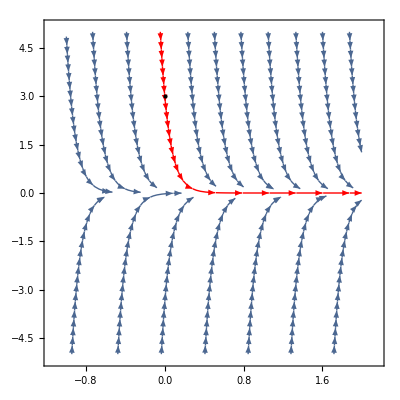

```mathematica
StreamPlot[{1,-v/((0.09) (1))},{t,-1,2},{v,-5,5},
	Axes->True,
	StreamPoints->{{{{0,3},Red},Automatic}}, 
	Epilog->{Black, PointSize[Medium],Point[{0,3}]}]
```

como era de esperarse a medida que el tiempo avanza el voltaje empieza a hacerse cero, para saber entonces como es el voltaje con exactitud tenemos que resolver esta EDO homogenea, dividimos entre c para llevarla  a la forma estándar del factor integrante

```mathematica
(*multilplicamos a ambos lados por 1/c*)
(1/c) *#&/@ (v[t]/r+c v'[t]==0) //FullSimplify
```

v[t]/(c r)+v'[t]==0

finalmente calculando el factor integrante y resolviendo la EDO

```mathematica
p[t_]:=1/(c*r)
μ = ⅇ^Integrate[p[t],t]
```

ⅇ^(t/(c r))

```mathematica
D[μ v[t],t]== μ * 0 //FullSimplify
```

(ⅇ^(t/(c r)) (v[t]+c r v'[t]))/(c r)==0

integrando a ambos lados y despejando v[t] tenemos:

```mathematica
SetAttributes[c1,Constant] 
ecu4 = ∫(ⅇ^(t/(c r)) (v[t]+c r v'[t]))/(c r)ⅆt ==∫0 ⅆt+c1
Solve[ecu4,v[t]][[1,1]]
```

ⅇ^(t/(c r)) v[t]==c1

v[t]→c1 ⅇ^(-t/(c r))

despejando el valor de la constante entonces tenemos

```mathematica
v[t]->ⅇ^(-t/(c r)) c1//.{v[t]-> 3, t-> 0}
```

3→c1

como era de esperarse la constante c1 corresponde a el valor v0 osea al valor de voltaje inicial, la ecuacion y su grafica finalmente queda...................rojo

```mathematica
v[t]->ⅇ^(-t/(c r)) c1//.{c1-> 3}
```

v[t]→3 ⅇ^(-t/(c r))

Gráfica de la solución particular y la familia uniparamétrica de soluciones

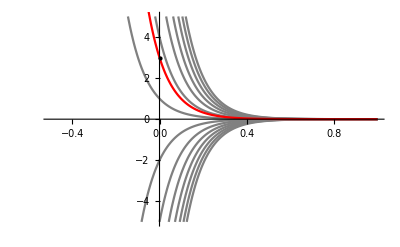

```mathematica
(*Tabla de soluciones para diferentes valores de c*)
Tabla=Table[ⅇ^(-t/((0.09) (1))) c1,{c1,-20,20,3}]; 
Show[
	Plot[Tabla,{t,-0.5,1},PlotStyle->Gray, PlotRange->{-5,5}],
	(*solucion particular*)
	Plot[3 ⅇ^(-t/((0.09) (1))),{t,-0.5,1},PlotStyle->Red],
	Graphics[{Black, PointSize[Large],Point[{0,3}]}]
]
```

#### Respuesta de un circuito LC

Supongamos que se conecto un circuito RL de la siguiente forma hasta que por el inductor fluya una corriente

Una vez cargado el capacitor  y conectamos el switch de la sigiente forma

-Graphics-

supongamos que  i_0 =  1 Amper, L = 0.01h y r =  1Ω, así que i[0] = i_0 queremos saber que ocurre con la corriente en la resistencia después de esto entonces por LVK tenemos

```mathematica
vr =  i*r; 
vl + vr ==0
(*ic  =  C v'[t]*)
```

i r+l i'[t]==0

de esta manera encontramos la ecuación diferencial de la corriente antes de resolverla, y aprovechando que este es un curso de ecuaciones diferenciales, haremos uso del teorema de existencia y unicidad, también esbozaremos un campo de pendientes para saber como se debe ver la solución.

Teorema de existencia y unicidad

despejando ⅆi/ⅆt

```mathematica
Solve[i r+l i'[t]==0==0, i'[t]][[1,1]]
f[t_,i_]:= -(i r)/l
D[(f[t,i]), i]
```

i'[t]→-(i r)/l

-r/l

de aquí se puede apreciar que se garantiza que existe soluciones en todos los reales donde  l != 0 y que ademas estas las soluciones son únicas.

### Campo de pendiente

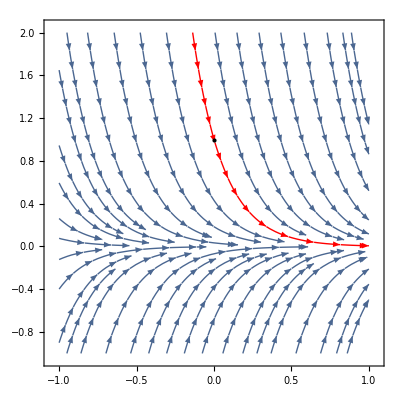

```mathematica
StreamPlot[{1,-(i (5))/(1)},{t,-1,1},{i,-1,2},
	Axes->True,
	StreamPoints->{{{{0,1},Red},Automatic}}, 
	Epilog->{Black, PointSize[Medium],Point[{0,1}]}]
```

como era de esperarse a medida que el tiempo avanza la corriente empieza a hacerse cero, para saber entonces como es la corriente con exactitud tenemos que resolver esta EDO homogénea, dividimos entre L para llevarla  a la forma estándar del factor integrante

```mathematica
(*multilplicamos a ambos lados por 1/l*)
(1/l) *#&/@ (i r+l i'[t]==0) //FullSimplify
```

(i r)/l+i'[t]==0

finalmente calculando el factor integrante y resolviendo la EDO

```mathematica
p[t_]:=r/l
μ = ⅇ^Integrate[p[t],t]
```

ⅇ^((r t)/l)

```mathematica
D[μ i[t],t]== μ * 0 //FullSimplify
```

(ⅇ^((r t)/l) (r i[t]+l i'[t]))/l==0

integrando a ambos lados y despejando v[t] tenemos:

```mathematica
ClearAll[c1]
SetAttributes[c1,Constant]
ecu5 = ∫(ⅇ^((r t)/l) (r i[t]+l i'[t]))/l ⅆt ==∫0 ⅆt+c1
Solve[ecu5,i[t]][[1,1]]
```

ⅇ^((r t)/l) i[t]==c1

i[t]→c1 ⅇ^(-(r t)/l)

despejando el valor de la constante entonces tenemos

```mathematica
i[t]->ⅇ^(-t/(c r)) c1//.{i[0]-> Subscript[i, 0], t-> 0}
```

i_0→c1

como era de esperarse la constante c1 corresponde a el valor i_0 osea al valor de voltaje inicial, la ecuacion y su grafica finalmente queda...................rojo

```mathematica
i[t]->c1 ⅇ^(-(r t)/l) c1//.{c1-> 1}
```

i[t]→ⅇ^(-(r t)/l)

Gráfica de la solución particular y la familia uniparamétrica de soluciones

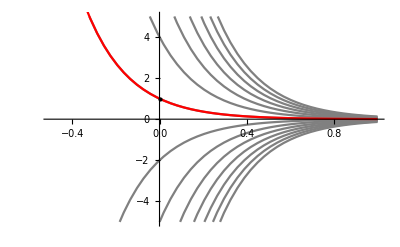

```mathematica
(*Tabla de soluciones para diferentes valores de c*)
Tabla=Table[ⅇ^(-((5) t)/(1)) c1,{c1,-20,20,3}]; 
Show[
	Plot[Tabla,{t,-0.5,1},PlotStyle->Gray, PlotRange->{-5,5}],
	(*solucion particular*)
	Plot[ⅇ^(-((5) t)/(1)),{t,-0.5,1},PlotStyle->Red],
	Graphics[{Black, PointSize[Large],Point[{0,1}]}]
]
```

#### Respuesta de un circuito LC

suponemos que incialmente el capacitor tiene un voltaje v_0, por LVK

```mathematica
ClearAll[c]
vc =1/c∫i[t]ⅆt;
vl+vc==0
```

(∫i[t]ⅆt)/c+l i'[t]==0

ahora vamos derivar una vez con respecto a t para eliminar la integral

```mathematica
D[(∫i[t]ⅆt)/c+l i'[t]==0,t] //TraditionalForm
ecua5 = %;
```

(i(t))/c+l i''(t)==0

ahora tenemos una ecuación diferencial homogénea de segundo orden la cual dividiremos entre l para llevarla a la forma estandar de coeficientes constantes.

```mathematica
(1/l) *#&/@ ecua5 //FullSimplify //TraditionalForm
```

(i(t))/(c l)+i''(t)==0

asumimos la respuesta de tipo c1ⅇ^rx+ c2ⅇ^rx donde r es la  raíz de la ecuación homogénea asociada

```mathematica
Solve[m^2+0m+1/(c*l)==0,m]//FullSimplify
```

{{m→-ⅈ/(√c √l)},{m→ⅈ/(√c √l)}}

para simplificar las cosas 1/(√c √L)lo renombraremos como  ω_0 donde ω_0 sera la frecuencia natural del sistema

```mathematica
{{m->-ⅈ/(√c √l)},{m->ⅈ/(√c √l)}}//.{1/(√c √l)-> Subscript[ω, 0]}
```

{{m→-ⅈ ω_0},{m→ⅈ ω_0}}

como obtuvimos respuestas imaginarias de la forma r = a + bⅈ entonces la solución es de tipo ⅇ^ax(c1 Sin(bt)+c2 Cos(bt)),

```mathematica
i[t] == ⅇ^(0x)(c1 Sin[Subscript[ω, 0] t]+c2 Cos[Subscript[ω, 0] t]) //FullSimplify
```

c2 Cos[t ω_0]+c1 Sin[t ω_0]==i[t]

para encontrar los valores de c1 y c2 usaremos las condiciones iniciales v(0)==v_0 i(0) == 0, como v_0==Lⅆi/ⅆt entonces , i'(t)=v_0/L

```mathematica
c2 Cos[t Subscript[ω, 0]]+c1 Sin[t Subscript[ω, 0]]==i[t]//.{i[t]-> 0, t-> 0}
```

c2==0

usando la segunda condición inicial i'(t)=v_0/L

```mathematica
D[c1 Sin[t Subscript[ω, 0]]==i[t],t]
ecua6 = c1 Cos[t Subscript[ω, 0]] Subscript[ω, 0]==i'[t]//.{i'[t]->Subscript[v, 0]/l,t-> 0}
Solve[ecua6,c1]
```

c1 Cos[t ω_0] ω_0==i'[t]

c1 ω_0==v_0/l

{{c1→v_0/(l ω_0)}}

simplificando la expresión

```mathematica
√(1/(l c)) l ==  √(l^2/(l c))== √(l/c) ->  1/(l Subscript[ω, 0]) == √(c/l)
```

Finalmente remplazado y obteniendo el resultado

i[t] == √(c/l)v_0 Sin(ω_0 t)

ecuación del voltaje sabemos que el voltaje = l i'[t]

```mathematica
l D[√(c/l)Subscript[v, 0] Sin[Subscript[ω, 0] t],t]
```

√(c/l) l Cos[t ω_0] v_0 ω_0

dando algunos valores para ver sus gráficas

```mathematica
l = 1;
c = 1/4;
w = √(1/(l*c))
Subscript[v, 0] = 10;

Print["corriente"]
i[t_]:=√(c/l)Subscript[v, 0] Sin[w t]
i[t]
Print["voltaje"]
v[t_]:=√(c/l) l Cos[t w] Subscript[v, 0] w
v[t]
```

2

corriente

5 Sin[2 t]

voltaje

10 Cos[2 t]

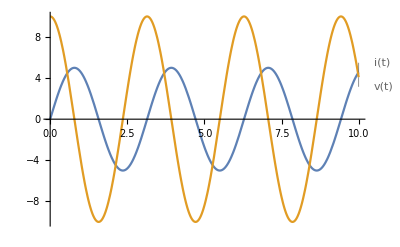

```mathematica
Plot[{i[t], v[t]},{t,0,10},PlotLabels->"Expressions"]
```